## Phases and Coefficiets

```mathematica
imgsize=700;
```

```mathematica
SetDirectory@NotebookDirectory[]
```

/Users/leima/GitHub/NeuPhysics/codebase/mma/matter

```mathematica
ClearAll[n1M,n2M,k1M,k2M,a1M,a2M,phaseList,coeffList,coeffListRe,coeffListIm,coeffListAbs,list0,list1,list2,list3,list4,n2List1,n1List2,n2List3,n1List4,meshStyle,parList,k1A,k2A,a1A,a2A,range,range2];
```

Parameters

```mathematica
thetamV=Pi/5;
k1V=0.3;
k2V=0.7;
a1V=0.1(k1V)^(-5/3);
a2V=0.1(k1V)^(-5/3);
phi1V=0;
phi2V=0;
```

Building Functions

```mathematica
bCoef[n1_,n2_,k1_,k2_,a1_,a2_]:=-(-I)^(n1+n2)Tan[2thetamV]/2 n1 k1 BesselJ[n1,a1/k1 Cos[2thetamV]]BesselJ[n2,a2/k2 Cos[2thetamV]]
```

Function to generate the listdensityplots of the phases and coefficients

```mathematica
coefDenPlt[k1_,k2_,a1_,a2_,range_]:=Module[{n1M,n2M,k1M,k2M,a1M,a2M,phaseList,coeffList,coeffListRe,coeffListIm,coeffListAbs,list0,list1,list2,list3,list4,n2List1,n1List2,n2List3,n1List4,meshStyle,parList},
meshStyle=None;
k1M=k1;
k2M=k2;
a1M=a1;
a2M=a2;

phaseList=Flatten[Table[{n1,n2,Abs[n1 k1M+ n2 k2M-1]},{n1,-range,range},{n2,-range,range}],1];
coeffList=Flatten[Table[{n1,n2,bCoef[n1,n2,k1M,k2M,a1M,a2M]+bCoef[n2,n1,k2M,k1M,a2M,a1M]},{n1,-range,range},{n2,-range,range}],1];
coeffListRe=Flatten[Table[{n1,n2,Log@Re[bCoef[n1,n2,k1M,k2M,a1M,a2M]+bCoef[n2,n1,k2M,k1M,a2M,a1M]]},{n1,-range,range},{n2,-range,range}],1];
coeffListIm=Flatten[Table[{n1,n2,Log@Im[bCoef[n1,n2,k1M,k2M,a1M,a2M]+bCoef[n2,n1,k2M,k1M,a2M,a1M]]},{n1,-range,range},{n2,-range,range}],1];
coeffListAbs=Flatten[Table[{n1,n2,Log@Abs[bCoef[n1,n2,k1M,k2M,a1M,a2M]+bCoef[n2,n1,k2M,k1M,a2M,a1M]]},{n1,-range,range},{n2,-range,range}],1];
lineRWA=(1-n1 k1M)/k2M;

parList=Text["Parameters:\n k1="<>ToString[k1M]<>";\n k2="<>ToString[k2M]<>";\n a1="<>ToString[a1M]<>";\n a2="<>ToString[a2M]<>";\n\n"];

Grid[
{{
Show[ListDensityPlot[phaseList,Mesh->meshStyle,FrameLabel->{"n1","n2"},ColorFunction->"AvocadoColors",PlotLegends->All,ImageSize->imgsize,PlotLabel->"Phases" ,InterpolationOrder->0],Plot[lineRWA,{n1,-range,range},ImageSize->imgsize,PlotRange->{{-range,range},{-range,range}}]]
,
Show[ListDensityPlot[coeffListAbs,Mesh->meshStyle,FrameLabel->{"n1","n2"},ColorFunction->"AvocadoColors",PlotLegends->All,ImageSize->imgsize,PlotLabel->"Absolute Value of The Coefficient" ,InterpolationOrder->0],Plot[lineRWA,{n1,-range,range},ImageSize->imgsize,PlotRange->{{-range,range},{-range,range}}]]
},{
Show[ListDensityPlot[coeffListRe,Mesh->meshStyle,FrameLabel->{"n1","n2"},ColorFunction->"AvocadoColors",PlotLegends->All,ImageSize->imgsize,PlotLabel->"Real Part of The Coefficient" ,InterpolationOrder->0],Plot[lineRWA,{n1,-range,range},ImageSize->imgsize,PlotRange->{{-range,range},{-range,range}}]],
Show[ListDensityPlot[coeffListIm,Mesh->meshStyle,FrameLabel->{"n1","n2"},ColorFunction->"AvocadoColors",PlotLegends->All,ImageSize->imgsize,PlotLabel->"Imaginary Part of The Coefficient" ,InterpolationOrder->0],Plot[lineRWA,{n1,-range,range},ImageSize->imgsize,PlotRange->{{-range,range},{-range,range}}]]
}}
]
]
```

Function to plot the change of coeffcients along a line of the n1-n2 plane.

```mathematica
coefSlicings[k1_,k2_,a1_,a2_,range_,range2_]:=Module[{n1M,n2M,k1M,k2M,a1M,a2M,coeffList,coeffListRe,coeffListIm,coeffListAbs,list0,list1,list2,list3,list4,n2List1,n1List2,n2List3,n1List4,meshStyle},
meshStyle=None;
k1M=k1;
k2M=k2;
a1M=a1;
a2M=a2;
coeffList=Flatten[Table[{n1,n2,bCoef[n1,n2,k1M,k2M,a1M,a2M]+bCoef[n2,n1,k2M,k1M,a2M,a1M]},{n1,-range,range},{n2,-range,range}],1];
coeffListRe=Flatten[Table[{n1,n2,Log@Re[bCoef[n1,n2,k1M,k2M,a1M,a2M]+bCoef[n2,n1,k2M,k1M,a2M,a1M]]},{n1,-range,range},{n2,-range,range}],1];
coeffListIm=Flatten[Table[{n1,n2,Log@Im[bCoef[n1,n2,k1M,k2M,a1M,a2M]+bCoef[n2,n1,k2M,k1M,a2M,a1M]]},{n1,-range,range},{n2,-range,range}],1];
coeffListAbs=Flatten[Table[{n1,n2,Log@Abs[bCoef[n1,n2,k1M,k2M,a1M,a2M]+bCoef[n2,n1,k2M,k1M,a2M,a1M]]},{n1,-range,range},{n2,-range,range}],1];
list0=Table[{n1,Abs[bCoef[n1,Round[(1-n1 k1M)/k2M],k1M,k2M,a1M,a2M]+bCoef[Round[(1-n1 k1M)/k2M],n1,k2M,k1M,a2M,a1M]]},{n1,-range,range}];
n2List1=0;
list1=Table[{n1,Abs[bCoef[n1,n2List1,k1M,k2M,a1M,a2M]+bCoef[n2List1,n1,k2M,k1M,a2M,a1M]]},{n1,-range,range}];
n1List2=0;
list2=Table[{n2,Abs[bCoef[n1List2,n2,k1M,k2M,a1M,a2M]+bCoef[n2,n1List2,k2M,k1M,a2M,a1M]]},{n2,-range,range}];
n2List3=Round[range/2];
list3=Table[{n1,Abs[bCoef[n1,n2List3,k1M,k2M,a1M,a2M]+bCoef[n2List3,n1,k2M,k1M,a2M,a1M]]},{n1,-range,range}];
n1List4=Round[range/2];
list4=Table[{n2,Abs[bCoef[n1List4,n2,k1M,k2M,a1M,a2M]+bCoef[n2,n1List4,k2M,k1M,a2M,a1M]]},{n2,-range,range}];

Grid[{{ListLogPlot[list0,ImageSize->imgsize,Frame->True,PlotLabel->"Slicings",Joined->True,PlotStyle->{Dotted,Red},PlotMarkers->{Automatic, Small},PlotLegends->Placed[{"RWA"},{Top,Center}],PlotRange->{{-range2,range2},Automatic},GridLines->{{{Round[1/k1M],Dashed},{Round[(1-Round[1/k2M] k2M)/k1M],Red}}, {1}}]
,
ListLogPlot[{list0,list1,list2,list3,list4},ImageSize->imgsize,Frame->True,PlotLabel->"Slicings",Joined->True,PlotStyle->{{Dotted,Red},Blue,Black,Gray,Magenta},PlotMarkers->{Automatic, Small},PlotLegends->Placed[{"RWA","n2="<>ToString[n2List1],"n1="<>ToString[n1List2],"n2="<>ToString[n2List3],"n1="<>ToString[n1List4]},{Top,Center}]]}}]

]
```

Test result for some example data.

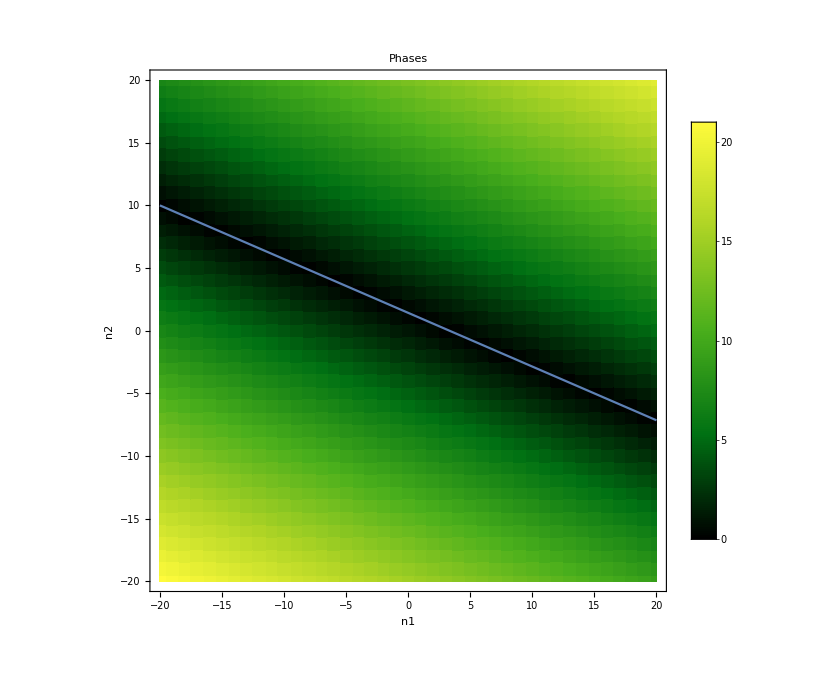
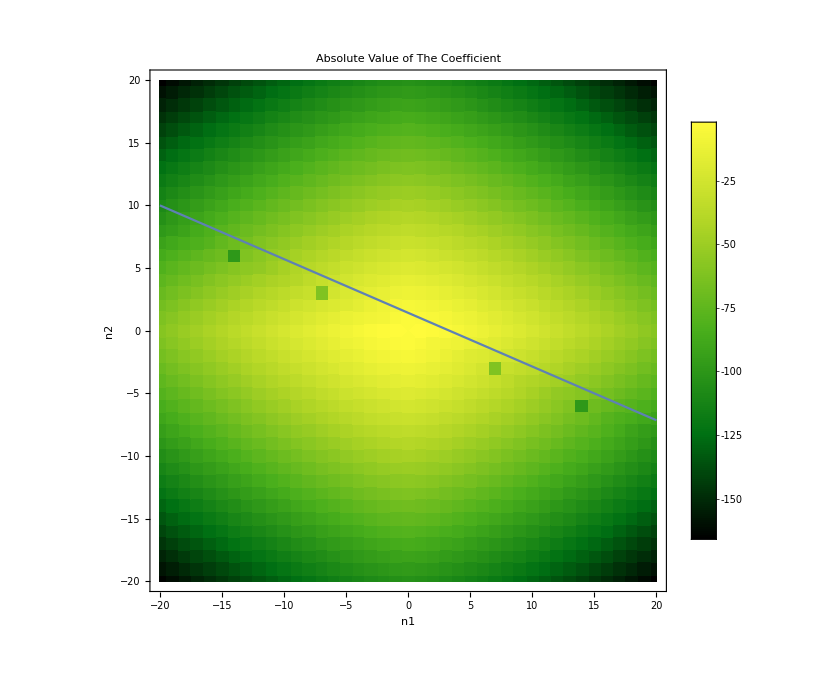
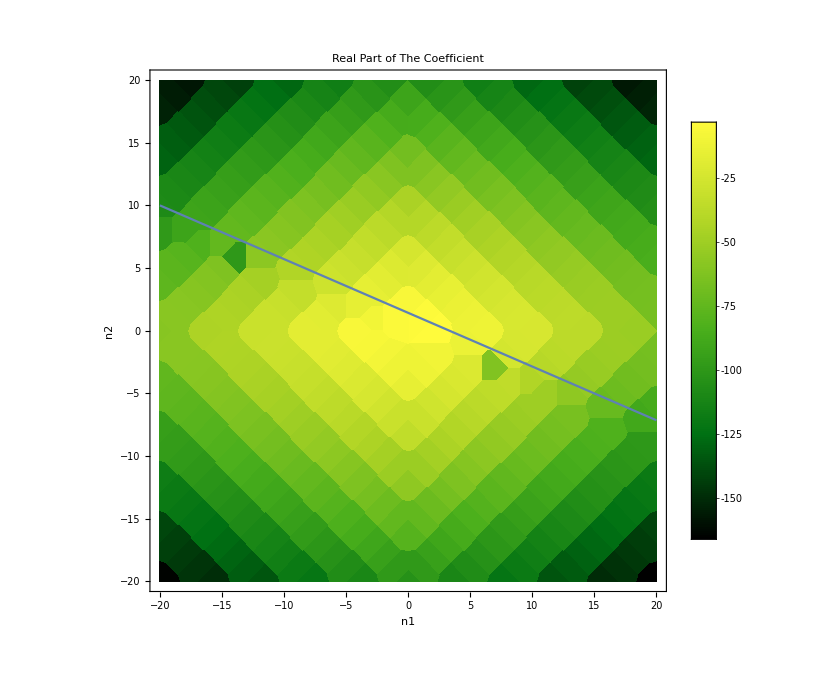
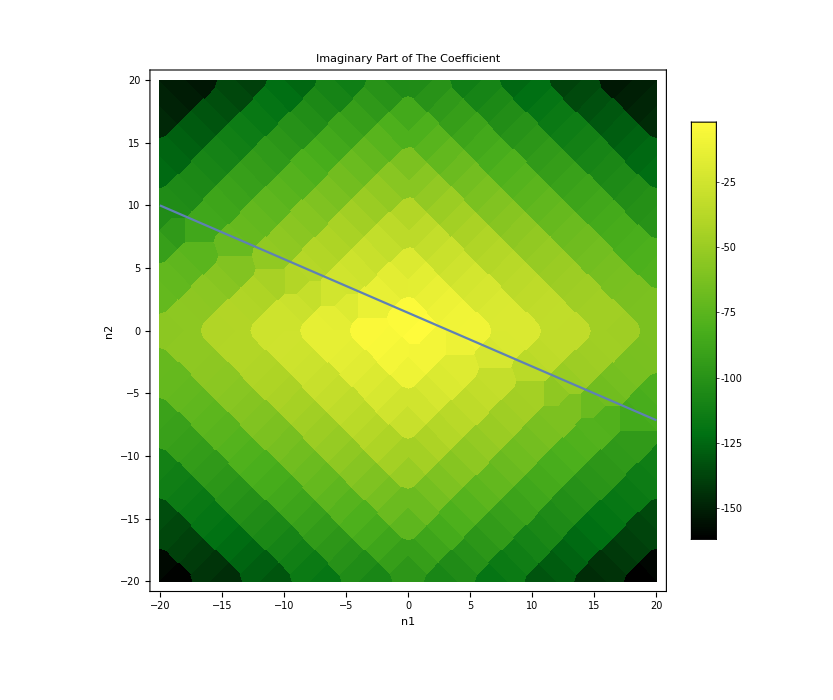
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
Module[{k1A,k2A,a1A,a2A,range,range2},
k1A=k1V;
k2A=k2V;
a1A=0.1(k1V)^(-5/3);
a2A=0.1(k2V)^(-5/3);
range=20;
range2=5 ;
Grid[{{
coefDenPlt[k1A,k2A,a1A,a2A,range]
},{
coefSlicings[k1A,k2A,a1A,a2A,range,range2]
}}]
]
(*Export["export/stimulated-2-freq-coef-non-approx-a2-larger-non-mesh.png",%]*)
```

## Compare with Previous calculations

We had a case where adding 1 and 2 will change the result but adding 3 doesn’t. They match the exact data when 4th order is added.

### First Case

k1=0.3;
k2=0.99;
a1=0.2*0.1(k1)^(-5/3);
a2=0.1(k2)^(-5/3);

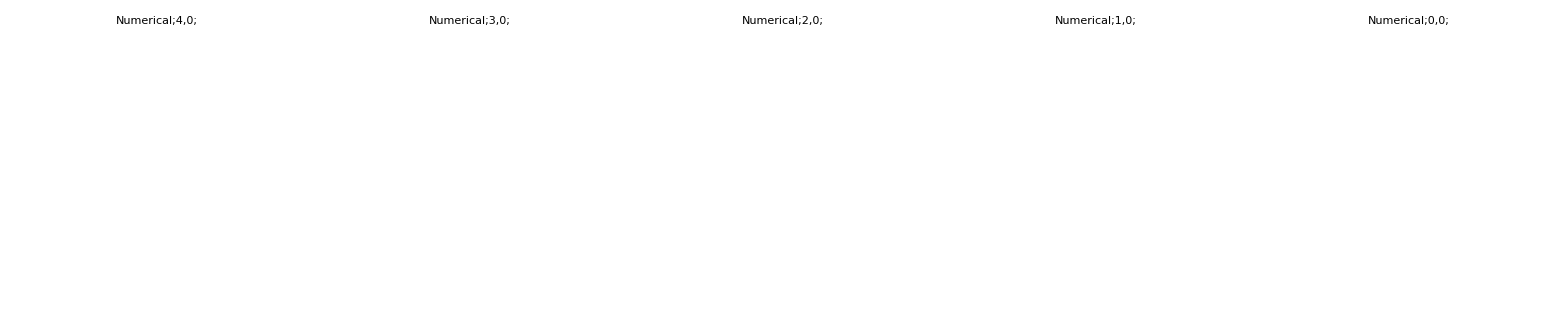

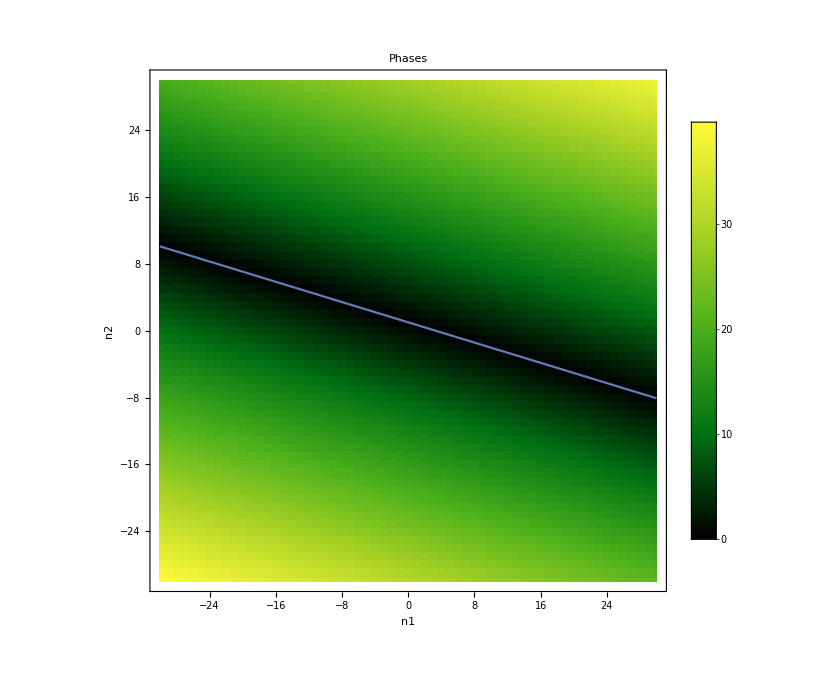
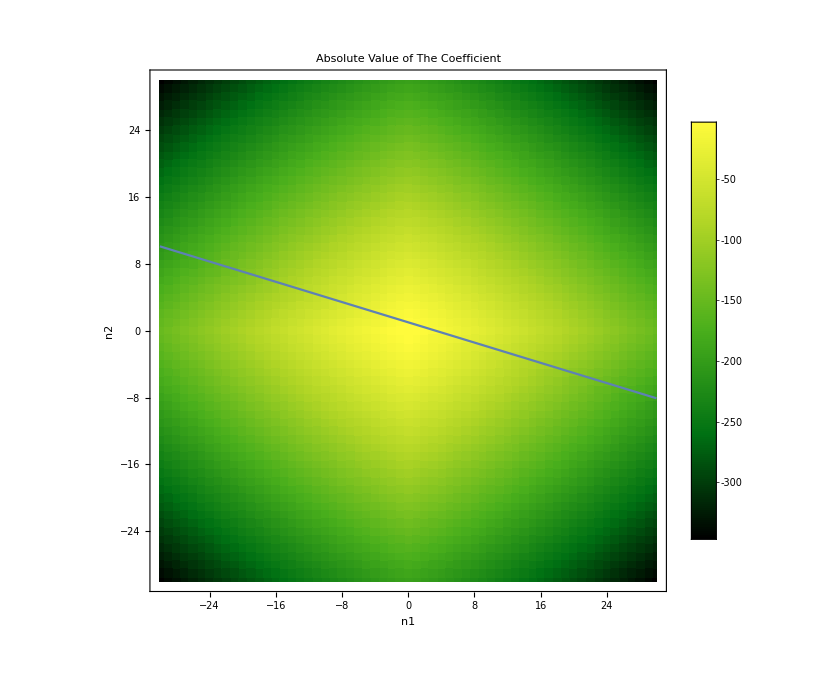
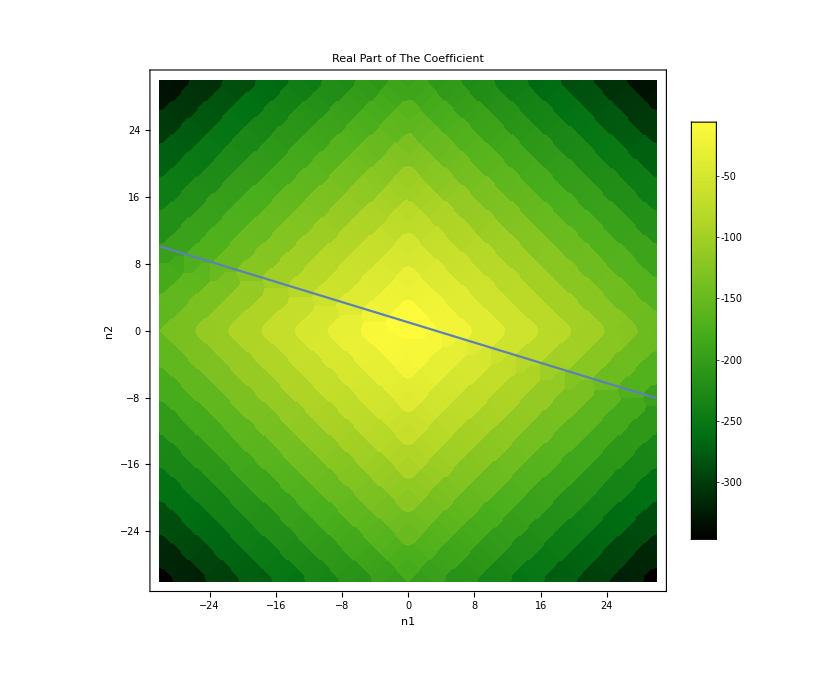
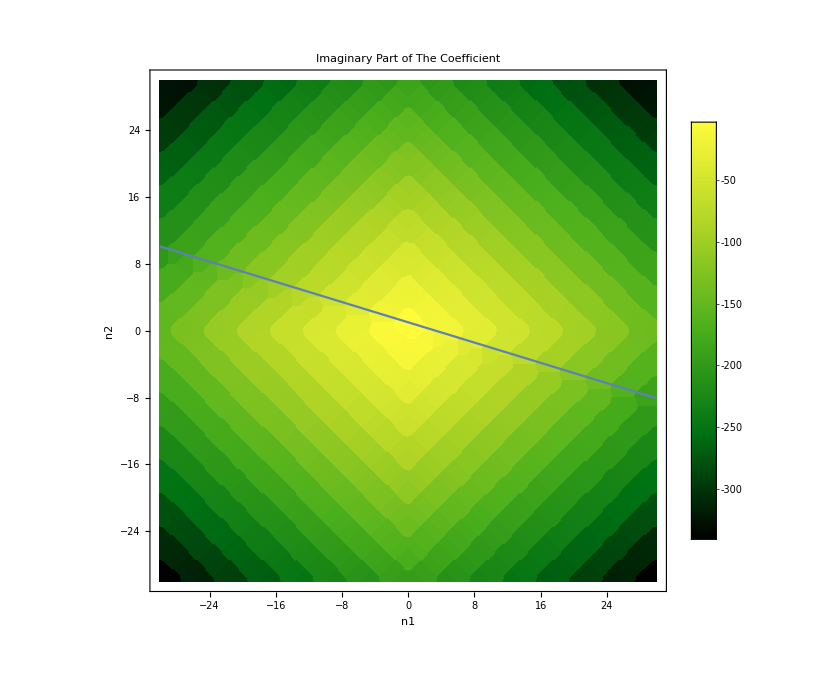
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
Module[{k1A,k2A,a1A,a2A,range,range2},
k1A=0.3;
k2A=0.99;
a1A=0.2*0.1(k1A)^(-5/3);
a2A=0.1(k2A)^(-5/3);
range=30;
range2=5 ;
Grid[{{
coefDenPlt[k1A,k2A,a1A,a2A,range]
},{
coefSlicings[k1A,k2A,a1A,a2A,range,range2]
}}]
]
```

### Second Case

k1=0.3;
k2=0.99;
a1=0.4*0.1(k1)^(-5/3);
a2=0.1(k2)^(-5/3);

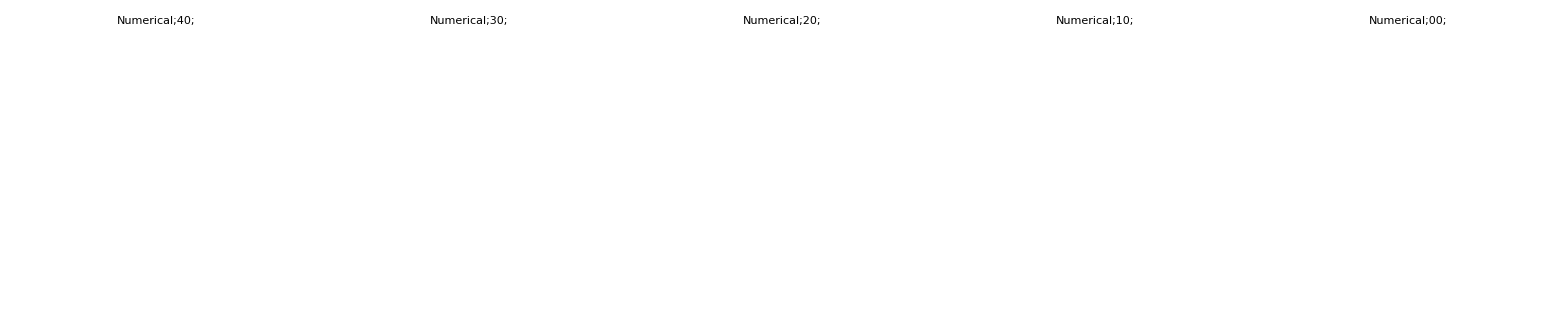

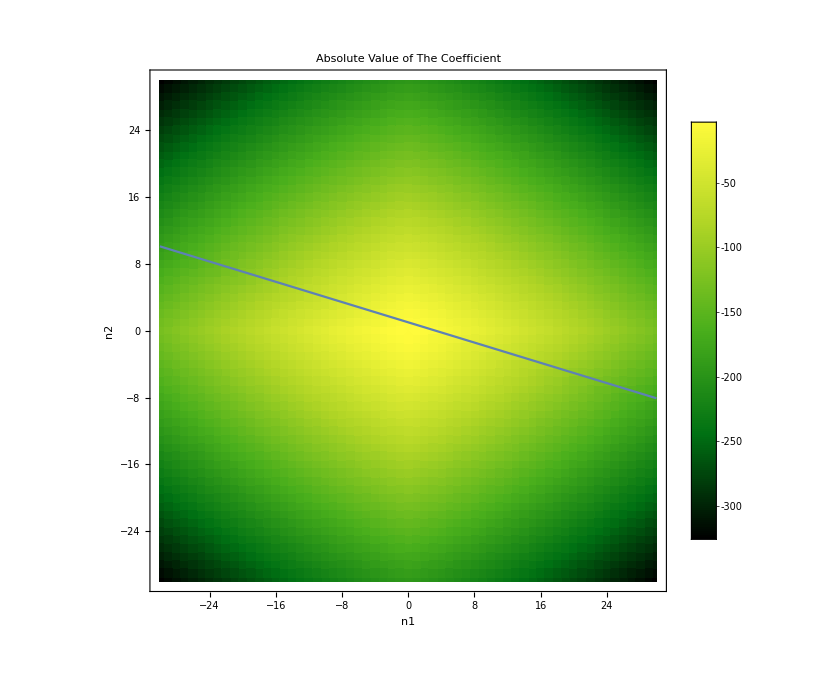
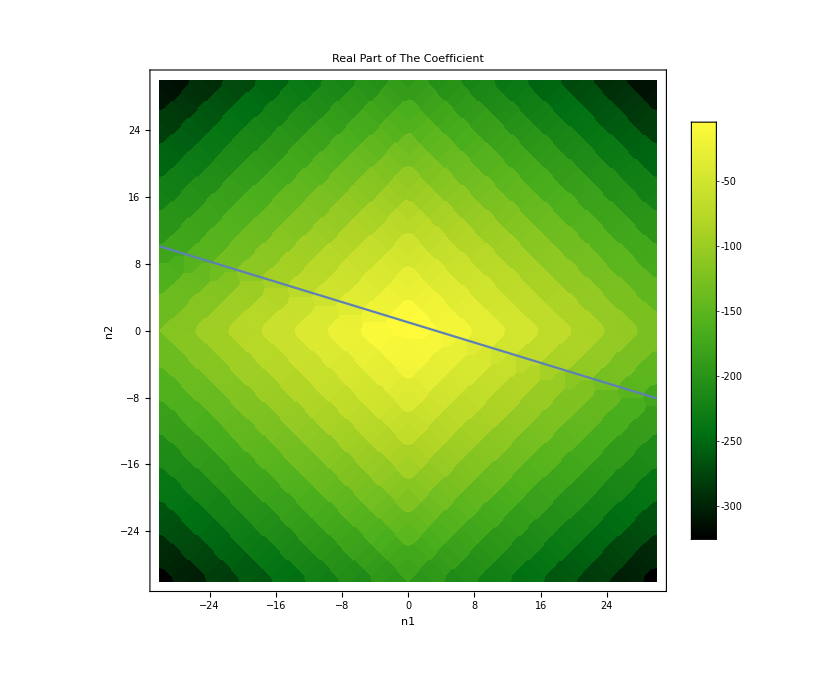
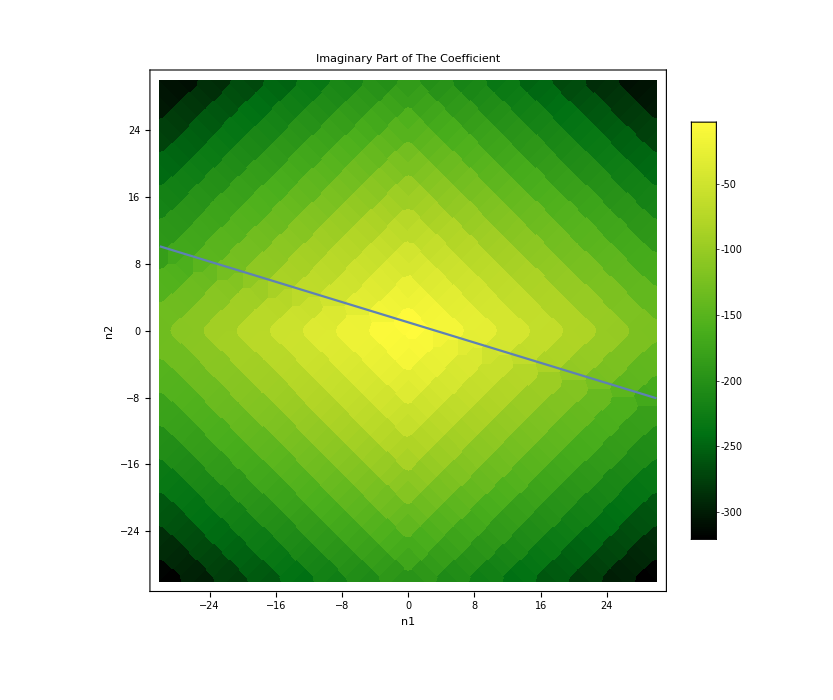
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
Module[{k1A,k2A,a1A,a2A,range,range2},
k1A=0.3;
k2A=0.99;
a1A=0.4*0.1(k1A)^(-5/3);
a2A=0.1(k2A)^(-5/3);
range=30;
range2=10 ;
Grid[{{
coefDenPlt[k1A,k2A,a1A,a2A,range]
},{
coefSlicings[k1A,k2A,a1A,a2A,range,range2]
}}]
]
```

#### Resonances